# Matter Power Spectrum: wCDM

```mathematica
Quit[]
```

## Data

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[8]; (* To use all the available kernels *)
```

### Data

```mathematica
wCDMfiles="/Users/cosmology/class_public/output/wCDM/";
Pkw08cs20001=Import[wCDMfiles<>"w_0.8_cs2_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
Pkw09cs20001=Import[wCDMfiles<>"w_0.9_cs2_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
Pkw1cs20001=Import[wCDMfiles<>"w_1_cs2_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
Pkw11cs20001=Import[wCDMfiles<>"w_1.1_cs2_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
Pkw12cs20001=Import[wCDMfiles<>"w_1.2_cs2_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
```

```mathematica
wlist={-0.8,-0.9,-1,-1.1,-1.2};
Pkw08=Table[{Pkw08cs20001[[i,1]],wlist[[1]],Pkw08cs20001[[i,2]]},{i,1,Length[Pkw08cs20001]}];
Pkw09=Table[{Pkw09cs20001[[i,1]],wlist[[2]],Pkw09cs20001[[i,2]]},{i,1,Length[Pkw09cs20001]}];
Pkw1=Table[{Pkw1cs20001[[i,1]],wlist[[3]],Pkw1cs20001[[i,2]]},{i,1,Length[Pkw1cs20001]}];
Pkw11=Table[{Pkw11cs20001[[i,1]],wlist[[4]],Pkw11cs20001[[i,2]]},{i,1,Length[Pkw11cs20001]}];
Pkw12=Table[{Pkw12cs20001[[i,1]],wlist[[5]],Pkw12cs20001[[i,2]]},{i,1,Length[Pkw12cs20001]}];
```

```mathematica
MockData=Drop[Join[Pkw08,Pkw09,Pkw1,Pkw11,Pkw12],{1,-1,2}];
Dimensions[MockData] (* Dimensions of the dataset *)
```

{285,3}

#### Fitting Formulae

```mathematica
(* All the formulas are extracted from EH97I[9709112 v1] paper, unless stated.*)
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
h=0.67810;
(* See Eq. (11) *)
a1[ωm_]:=(46.9ωm)^0.670 (1+(32.1 ωm)^-0.532)
a2[ωm_]:=(12.0 ωm)^0.424 (1+(45.0 ωm)^-0.582) 
αc[ωb_,ωm_]:=a1[ωm]^(-ωb/ωm)*a2[ωm]^(-(ωb/ωm)^3)
(* See Eq. (12) *)
b1[ωm_] := 0.944 (1+(458 ωm)^-0.708)^-1 
b2[ωm_]:=(0.395 ωm)^-0.0266 
βc[ωb_,ωm_]:=(1+b1[ωm](((ωm - ωb)/ωm)^b2[ωm]-1))^-1 
(* Redshift at drag epoch -> See Eq. (4) *)
b1d[ωm_]:=0.313 ωm^-0.419 (1 + 0.607 ωm^0.674) 
b2d[ωm_]:=0.238 ωm^0.223 
zd[ωb_,ωm_]:=1291*ωm^0.251/(1 + 0.659 ωm^0.828)(1 + b1d[ωm] ωb^b2d[ωm]) 
zeq[ωm_]:=2.5*10^4 ωm*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (2) *)
keq[ωm_]:=7.46*10^-2 ωm*Θ^-2  (* scale at equilibrium epoch -> See Eq. (3) *)
q[k_,ωm_] := k/(13.41 keq[ωm])  (* See Eq. (10) *)
R[z_,ωb_]:=31.5*ωb*Θ^-4*(z/10^3)^-1  (* Baryon-Photon ratio -> See Eq. (5) *)
yEH[z_,ωm_]:=(1+zeq[ωm])/(1+z) (* Useful variable for calculations in LS limit -> See Eq.(8.20) in Dodelson 2 *)
(* Sub-horizon solution of the Mezsaros' eq. -> See Eq. (8.63) in Dodelson 2 *)
G[z_,ωm_]:=yEH[z, ωm] (-6 √(1+yEH[z,ωm])+(2+3yEH[z,ωm])Log[(√(1 + yEH[z, ωm])+1)/(√(1 + yEH[z, ωm])-1)]) 
(* Silk damping scale -> See Eq. (7) *)
ksilk[ωb_,ωm_]:=1.6 ωb^0.52*ωm^0.73(1+(10.4 ωm)^-0.95) (* [(Mpc^-1)]*)
βnode[ωm_]:=8.41*ωm^0.435 (* Shifting of nodes parameter -> See Eq. (23) *)
(* Sound horizon at drag epoch -> See Eq. (6) *)
s[ωb_,ωm_]:=2/(3 keq[ωm])√(6/R[zeq[ωm],ωb])Log[(√(1+R[zd[ωb,ωm],ωb])+√(R[zd[ωb,ωm],ωb]+R[zeq[ωm],ωb]))/(1+√R[zeq[ωm],ωb])]
st[k_,ωb_,ωm_]:=s[ωb,ωm]/((1+(βnode[ωm]/(k*s[ωb, ωm]))^3)^(1/3)) (* Shifting of oscillations nodes -> See Eq. (22) *)
(* Amplitude of small scale contributions -> See Eq. (14) *)
αb[ωb_,ωm_]:=2.07*keq[ωm]*s[ωb,ωm] (1+R[zd[ωb,ωm],ωb])^(-3/4)G[yEH[zd[ωb,ωm],ωm], ωm] 

(* Small scale contributions -> See Eq. (24) *)
βb[ωb_,ωm_]:=0.5+ωb/ωm+(3-2 ωb/ωm) √((17.2 ωm)^2+1)
f[k_,ωb_,ωm_]:=1/(1 + ((k*s[ωb, ωm])/5.4)^4) (* See Eq (18) *)
Cf[k_,ωb_,ωm_]:=14.2/αc[ωb,ωm]+386/(1 + 69.9*q[k,ωm]^1.08) (* See Eq. (20) *)
Cfαc1[k_,ωb_,ωm_]:=14.2 + 386/(1 + 69.9*q[k,ωm]^1.08) (* Cf with αc = 1*)
(* See Eq. (19) *)
T0[k_,ωb_,ωm_]:=Log[ⅇ + 1.8*βc[ωb,ωm]*q[k,ωm]]/(Log[ⅇ+1.8 βc[ωb,ωm]*q[k,ωm]]+Cf[k,ωb,ωm]*q[k,ωm]^2)
(* See Eqs. (19) and (20) in EH97: T0(k, 1, βc) means αc = 1 in Eq. (20) *)
T01[k_,ωb_,ωm_]:=Log[ⅇ+1.8*βc[ωb,ωm]*q[k,ωm]]/(Log[ⅇ + 1.8 βc[ωb,ωm]*q[k,ωm]]+Cfαc1[k,ωb,ωm]*q[k,ωm]^2)
(* See Eq. (19) in EH97: T0(k, 1, 1) means αc = 1 in Eq. (20) and βc = 1 in Eq. (19) *)
T011[k_,ωb_,ωm_]:=Log[ⅇ+1.8*q[k,ωm]]/(Log[E+1.8*q[k,ωm]]+Cfαc1[k,ωb,ωm]*q[k,ωm]^2)
(* Transfer function for CDM -> See Eq. (17) *)
TcEH[k_,ωb_,ωm_]:=f[k,ωb,ωm]*T01[k,ωb,ωm]+(1-f[k,ωb,ωm])T0[k,ωb,ωm]
(* Transfer function for baryons -> See Eq. (21) *)
TbEH[k_,ωb_,ωm_]:=(T011[k, ωb, ωm]/(1+((k*s[ωb,ωm])/5.2)^2)+αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*s[ωb,ωm]))^3)ⅇ^(-(k/ksilk[ωb,ωm])^1.4))Sin[k*st[k,ωb,ωm]]/(k*st[k,ωb,ωm])
(* Transfer function for CDM + baryons -> See Eq. (16) *)
TEH[k_,ωb_,ωm_] := (ωm - ωb)/ωm TcEH[k,ωb,ωm]+ωb/ωm TbEH[k,ωb,ωm]
```

```mathematica
(* From GA: x = k, y = Subscript[ω, m] -> See 2211.06393 *)
TGA[x_,y_]:=1/(1+59.09983473000389 (x/(y-ωb))^1.4917653903428132+4658.007645250978 (x/(y-ωb))^4.027553399922359+3170.788890492977 (x/(y-ωb))^6.0600043498512886+150.08874315951203 (x/(y-ωb))^7.284778673036612)^(1/4)
```

#### Comparison

```mathematica
(* Normalization factor from inflation -> Data from CLASS expalantaory.ini *)
ωb=0.02238280;
ωc=0.1201075;
ns=0.9619;
k^ns*TGA[k,ωb+ωc]^2/.k->Pkw08cs20001[[1,1]]
A.b4BSC=Pkw08cs20001[[1,2]]/%
k^ns*TEH[k*h,ωb,ωb+ωc]^2/.k->Pkw08cs20001[[1,1]]
A.b4EH=Pkw08cs20001[[1,2]]/%
```

0.0000164536

2.69004×10^6

0.000016454

2.68997×10^6

```mathematica
T1=k^ns*TEH[k*h,ωb,ωb+ωc]^2/.k->Pkw08cs20001[[1,1]];
T2=k^ns*TEH[k*h,ωb,ωb+ωc]^2/.k->Pkw09cs20001[[1,1]];
T3=k^ns*TEH[k*h,ωb,ωb+ωc]^2/.k->Pkw1cs20001[[1,1]];
T4=k^ns*TEH[k*h,ωb,ωb+ωc]^2/.k->Pkw11cs20001[[1,1]];
T5=k^ns*TEH[k*h,ωb,ωb+ωc]^2/.k->Pkw12cs20001[[1,1]];
CoeffPk={Pkw08cs20001[[1,2]]/T1,Pkw09cs20001[[1,2]]/T2,Pkw1cs20001[[1,2]]/T3,Pkw11cs20001[[1,2]]/T4,Pkw12cs20001[[1,2]]/T5}
```

{2.68997×10^6,2.85309×10^6,2.9961×10^6,3.12208×10^6,3.23363×10^6}

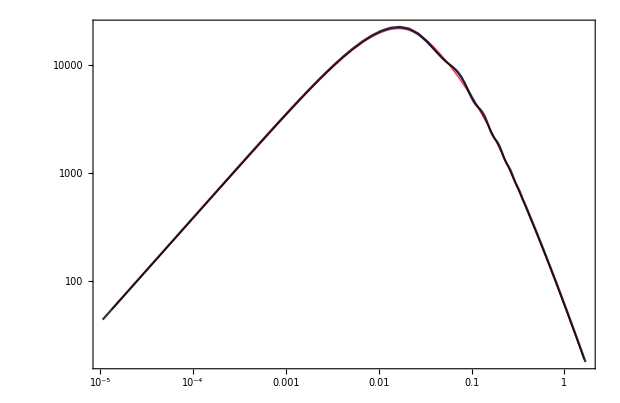

```mathematica
(* GAs formula gives a good approximated expression for P(k) *)
ListLogLogPlot[{Pkw08cs20001},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Opacity[0.8]],Directive[Black,Opacity[0.4]],Directive[Black,Opacity[0.6]],Directive[Black,Opacity[0.8]]},Frame->True,FrameStyle->BlackFrame,
FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc}/h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];
LogLogPlot[{A.b4EH*k^ns*TEH[k*h,ωb,ωb+ωc]^2,A.b4BSC*k^ns*TGA[k,ωb+ωc]^2},{k,MockData[[1,1]],MockData[[-1,1]]},PlotRange->All,PlotStyle->{Directive[Blue,Opacity[0.6],Thick],Directive[Red,Opacity[0.8],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{EH}"],(MaTeX[#,Magnification->1.2]&)/@Style["\\text{BSC}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendFunction->Frame],
{0.55,0.2}],ImageSize->620];
Show[{%,%%},PlotRange->All,ImageSize->620]
```

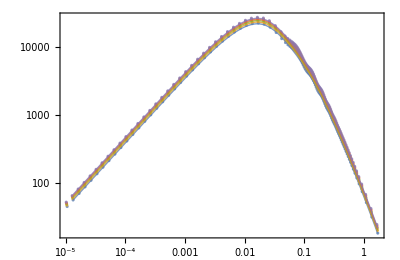

```mathematica
(* We just have to consider modifications in the normalization factor *)
ListLogLogPlot[{Pkw08cs20001,Pkw09cs20001,Pkw1cs20001,Pkw11cs20001,Pkw12cs20001},Joined->False,PlotRange->All,PlotStyle->{Directive[Opacity[0.8]],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.5]&)/@Style["w = -0.8"],
(MaTeX[#, Magnification -> 1.5] &)/@Style["w = -0.9"],
(MaTeX[#, Magnification -> 1.5] &)/@Style["w = -1"],
(MaTeX[#, Magnification -> 1.5] &)/@Style["w = -1.1"],
(MaTeX[#, Magnification -> 1.5] &)/@Style["w = -1.2"]},
 LegendLayout->{"Row", 5},LabelStyle->{Black,Bold,3},LegendMarkerSize->25,LegendFunction->Frame],{0.59,0.3}],ImageSize->Full];
LogLogPlot[{CoeffPk[[1]],CoeffPk[[2]],CoeffPk[[3]],CoeffPk[[4]],CoeffPk[[5]]}*k^ns*TGA[k,ωb+ωc]^2//Evaluate,{k,MockData[[1,1]],MockData[[57,1]]},PlotRange->All,PlotStyle->{Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];
Show[{%%,%},PlotRange->All,ImageSize->Full]
```

## Genetic Algorithm

## Grammar, Fitness Function, and Genetic Instructions

### Grammar

```mathematica
(* Possible operations. The proposal grammar depends on each specific problem *)
poly[x_]:=x
grammar={poly}; (* Array of operations *)
```

### Genetic Code

```mathematica
length=4; depth=4; (* Number of nucleotides and genes. Chromosomes will be 4x4 matrices *)

(* Ranges to compute random numbers specifying the expression of an individual *)
rang1={0,2};  (* Overall coefficient of the expression *)
rang2={1,Length[grammar]}; (* To choose an operation in the grammar *)
rang3={0,9}; (* Power of the expression *)
```

### Fitness Function

```mathematica
(* Accuracy of an Individual *)
AccGA[f_]:=AccGA[f]=Module[{temp,ft},
ft=(f/.{x->#1,y->#2})&; (* Individual *)
temp=Mean[Table[Abs[MockData⟦i,3⟧-ft[MockData⟦i,1⟧,MockData[[i,2]]]]/MockData⟦i,3⟧*100,{i,1,Length[MockData]}]]; (* Accuracy measure *)
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]] (* Space-Time constraints in the computation *)
```

## Genetic Operators

### Mutation

```mathematica
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]}; (* To decide where apply a mutation *)
mut=Which[
rep⟦2⟧==1,RandomReal[rang1], (* If rep⟦2⟧ == 1 -> modify the overall coefficient *)
rep⟦2⟧==2,RandomInteger[rang2], (* If rep⟦2⟧ == 2 -> modify the operation *)
rep⟦2⟧==3,RandomInteger[rang3]]; (* If rep⟦2⟧ == 3 -> modify the power of x *)
ReplacePart[kid,rep->mut]] (* Replace rep = {a, b} by mut = c in kid *)
```

### Crossover

```mathematica
cross[{kid1_,kid2_}]:=Module[{len},
len=RandomInteger[{1,length-1}]; (* Till length - 1 to not exceed the length of the chromosomes *)
{Join[kid1⟦1;;len⟧,kid2⟦(len+1);;-1⟧], (* Interchange of nucleotides *)
Join[kid1⟦(len+1);;-1⟧,kid2⟦1;;len⟧]}]
```

## Selection Scheme

### Tournament Selection

```mathematica
toursize=4; (* Participants in the tournament *)
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours], (* Take "tours" members from "fitnesses-set" at random *)
#1⟦1⟧>#2⟦1⟧&]⟦1,2⟧ (* Organize from greatest to smallest and take the individual with the best fit *)
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours], 
#1⟦1⟧>#2⟦1⟧&]⟦-1,2⟧ (* The same but taking the individual with the worst fit *)
```

## Genetic Algorithm

### Evolution of the Genetic Algorithm

```mathematica
selectionrate=0.3; (* Portion of the population to be sorted and replaced *)
(* Creator -> converts the chromosomes in "individuals" *)
funcPrim[y_,kid_,gram_]:=Sum[kid⟦i,1⟧( gram⟦kid⟦i,2⟧⟧@y)^kid⟦i,3⟧,{i,1,length}]
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2]; (* Around 1/3 of the population will be selected as the best *)
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={}; (* store: {fitness, individual, chromosome} *)

(* Progenitors -> Creation of "pop" chromosomes: 8 nucleotides for each gene and a total of 8 genes *)
chromosomes=Table[{RandomReal[rang1],RandomInteger[rang2],RandomInteger[rang3]},{pop},{length}];
t1=AbsoluteTime[];

(* "pigs" is a "prior". It is computed for all pop. Its form depends on the problem. Here, we are looking for modifications in the factor A introduced by MG theories *)
Do[
pigs=2.5*10^6(1+funcPrim[y,#,grammar])*x^ns*TGA[x,ωb+ωc]^2&/@chromosomes;
(* {-χ^2 for jth pig , counter j} sorted from the greatest to the smallest fitness *)
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[AccGA[pigs⟦j⟧],2,10^230],10^8,10^230],j},{j,1,Length[pigs]}],#1⟦1⟧>#2⟦1⟧&];

(* Append to bestfitperstep the greatest fitness, and its corresponding expression, and chromosomes *)
AppendTo[bestfitperstep,{fitness⟦1,1⟧,pigs⟦fitness⟦1,2⟧⟧,chromosomes⟦fitness⟦1,2⟧⟧}];

(* Selection of the best parents -> They are divided in pairs *)
p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];

(* Crossover of pairs *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes⟦p2⟦jj,1⟧⟧,chromosomes⟦p2⟦jj,2⟧⟧}], (* Worst are replaced by the children of the fittest *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

(* Mutation *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes⟦p2⟦jj,1⟧⟧],mutation[chromosomes⟦p2⟦jj,2⟧⟧]}, (* Worst are replaced by fittest mutations *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

prog`int++,{maxgens}];

If[verbose==True,
Print["Time taken: ",Round[AbsoluteTime[]-t1]," secs or ",Round[(AbsoluteTime[]-t1)/60], " mins"];
Print["Accuracy = ",Abs[fitness⟦1,1⟧]];
Print["Best-fit function is: "];
Print[bestfitperstep⟦-1,2⟧];
Speak["Listo el pollo"];];

bestfitperstep]
```

## Evolution

### Several Random Seeds

```mathematica
(* We try with several random seeds *)
generations=250;
SaveState={};
samples=10;
prog`int=0;prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
t0=AbsoluteTime[];
Do[GApop1[j]=GAevo[1234j,generations,100,0.7,0.35,False]//Quiet;
Print["Time: ", AbsoluteTime[]-t0];
AppendTo[SaveState,{GApop1[j]⟦-1,1⟧,1234j}]; (* Save the accuracy and random seed *)
Export["Save_State.txt",SaveState,"Table"];
prog`pop++;prog`int=0;,{j,1,samples}];
```

Time: 28.88134

Time: 58.369533

Time: 88.468422

Time: 118.17908

Time: 148.5008

Time: 178.80126

Time: 217.57358

Time: 246.82621

Time: 277.44504

Time: 307.00957

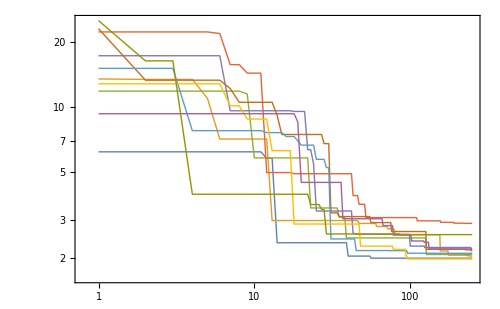

```mathematica
(* Plot the accuracy of GA solutions *)
Severalχ2=ListLogLogPlot[Table[GApop1[jj]⟦All,1⟧//Abs,{jj,1,samples}],Joined->True,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\text{Acc}\\%"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,PlotStyle->Thick,ImageSize->500]
```

```mathematica
DataSaved=Import["Save_State.txt","Data"];
```

```mathematica
DataSaved
```

{{-2.00362,1234},{-2.04897,2468},{-2.08326,3702},{-2.90018,4936},{-2.16825,6170},{-2.18888,7404},{-2.11035,8638},{-1.9873,9872},{-2.21079,11106},{-2.57404,12340}}

```mathematica
(* Best individual *)
Elite=Max[DataSaved⟦All,1⟧];
PosElite=Position[DataSaved,Elite];
DataSaved⟦PosElite⟦1,1⟧⟧ (* Determine the random seed and the accuracy of the winner *)
```

{-1.9873,9872}

```mathematica
AccGA[GApop1[PosElite⟦1,1⟧]⟦-1,2⟧] (* Accuracy of the winner *)
Limit[GApop1[PosElite⟦1,1⟧]⟦-1,2⟧,x->0] (* Correct limits of the winner *)
Limit[GApop1[PosElite⟦1,1⟧]⟦-1,2⟧,x->∞]
```

1.9873

0.

0.

### Long Run

```mathematica
generations=5000;
```

```mathematica
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, max generations, population, crossover-rate, mutation-rate, verbose (True/False)} *)
GApop=GAevo[9872,generations,100,0.7,0.35,True]//Quiet;(* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

Time taken: 552 secs or 9 mins

Accuracy = 1.96172

Best-fit function is:

(2.5×10^6 x^0.9619 (1+0.710636 y^3+1.88019 y^4+0.939217 y^5))/(√(1+1395.25 x^1.49177+2.37291×10^7 x^4.02755+1.19943×10^9 x^6.06+7.6116×10^8 x^7.28478))

```mathematica
Winner[α_,β_,x_,y_]:=(α x^β (1+0.7106356245167889 y^3+1.8801896647991612 y^4+0.939216799027307 y^5))/(√(1+1395.2489187744666 x^1.4917653903428132+2.3729066856033597*^7 x^4.027553399922359+1.1994340119292421*^9 x^6.0600043498512886+7.611601220332279*^8 x^7.284778673036612))
χ2Winner[α_,β_]:=Mean[Table[Abs[MockData⟦i,3⟧-Winner[α,β,MockData⟦i,1⟧,MockData[[i,2]]]]/MockData⟦i,3⟧*100,{i,1,Length[MockData]}]]
FindMinimum[χ2Winner[α,β],{{α,10^5,10^7},{β,0.9,1.1}}];
BFα=%[[2,1,2]];
BFβ=%%[[2,2,2]];
AccGA[Winner[BFα,BFβ,x,y]]
Winner[BFα,BFβ,x,y]
```

1.72292

(2.52395×10^6 x^0.96452 (1+0.710636 y^3+1.88019 y^4+0.939217 y^5))/(√(1+1395.25 x^1.49177+2.37291×10^7 x^4.02755+1.19943×10^9 x^6.06+7.6116×10^8 x^7.28478))

```mathematica
(* Check the correct limits of the GA solution *)
Limit[Winner[BFα,BFβ,x,y],x->0]
Limit[Winner[BFα,BFβ,x,y],x->∞]
```

0.

0.

```mathematica
(* We don't need to consider variations of Subscript[ω, c] here -> already encoded in Subscript[T, ΛCDM] *)
TGA[x,ωb+ωc]
```

1/((1+1395.25 x^1.49177+2.37291×10^7 x^4.02755+1.19943×10^9 x^6.06+7.6116×10^8 x^7.28478)^(1/4))

```mathematica
(* Constraint on y *)
Reduce[(1+0.7106356245167889 y^3+1.8801896647991612 y^4+0.939216799027307 y^5)>0]//Quiet
```

y>-1.68492

### Plots

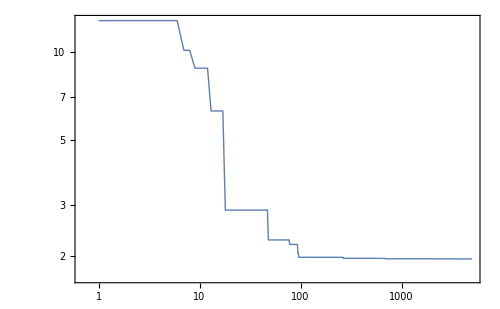

```mathematica
(* Plot of χ^2 over the generations *)
ListLogLogPlot[GApop[[All,1]]//Abs,Joined->True,
PlotRange->All,PlotStyle->Thick,
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\%\\mathrm{Acc}"},RotateLabel->True,BaseStyle->{FontFamily->"Times",FontSize->13},ImageSize->500]
```

```mathematica
accGA=Table[{MockData⟦i,1⟧,100*Abs[(1-Winner[BFα,BFβ,MockData⟦i,1⟧,MockData⟦i,2⟧]/MockData⟦i,3⟧)]},{i,1,Length[MockData]}];
```

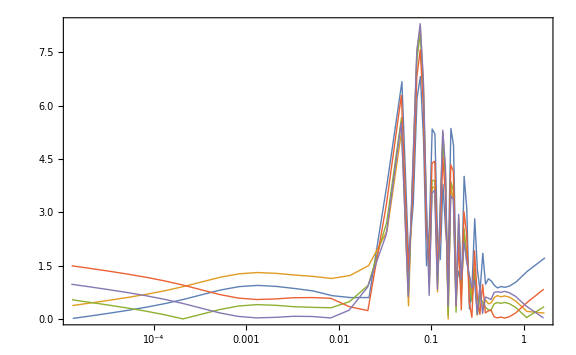

```mathematica
(* Accuracy as a function of k -> the factor 1/2 is required since we dropped some data points *)
ListLogLinearPlot[{accGA[[1;;1/2*114]],accGA[[114/2+1;;114]],accGA[[114+1;;3/2*114]],accGA[[3/2*114+1;;2*114]],accGA[[2*114+1;;5/2*114]]},Joined->True,PlotRange->{{MockData⟦1,1⟧,MockData⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"k \\, [h / \\text{Mpc}]","\\left|\\frac{P_{i, \\text{CLASS}} - P_{i, \\text{Analytical}}}{P_{i, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Thick},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.3]&)/@Style["w = -0.8"],
(MaTeX[#, Magnification -> 1.3] &)/@Style["w = -0.9"],
(MaTeX[#, Magnification -> 1.3] &)/@Style["w = -1"],
(MaTeX[#, Magnification -> 1.3] &)/@Style["w = -1.1"],
(MaTeX[#, Magnification -> 1.3] &)/@Style["w = -1.2"]},
 LegendLayout->{"Row", 5},LabelStyle->{Black,Bold,10},LegendMarkerSize->25,LegendFunction->Frame],{0.2,0.6}],
ImageSize->Large]
```

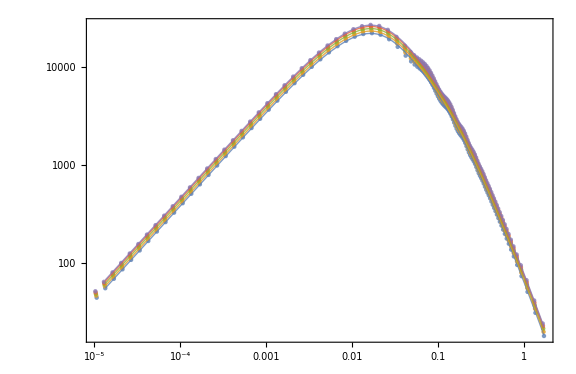

```mathematica
(* Best-Fit from the GA and the true function *)
ListLogLogPlot[{Pkw08cs20001,Pkw09cs20001,Pkw1cs20001,Pkw11cs20001,Pkw12cs20001},Joined->False,PlotRange->All,PlotStyle->{Directive[Opacity[0.8]],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.3]&)/@Style["w = -0.8"],
(MaTeX[#, Magnification -> 1.3] &)/@Style["w = -0.9"],
(MaTeX[#, Magnification -> 1.3] &)/@Style["w = -1"],
(MaTeX[#, Magnification -> 1.3] &)/@Style["w = -1.1"],
(MaTeX[#, Magnification -> 1.3] &)/@Style["w = -1.2"]},
 LegendLayout->{"Row", 5},LabelStyle->{Black,Bold,3},LegendMarkerSize->25,LegendFunction->Frame],{0.59,0.3}],ImageSize->Full];
LogLogPlot[{Winner[BFα,BFβ,x,-0.8],Winner[BFα,BFβ,x,-0.9],Winner[BFα,BFβ,x,-1],Winner[BFα,BFβ,x,-1.1],Winner[BFα,BFβ,x,-1.2]}//Abs//Evaluate,{x,MockData[[1,1]],MockData[[57,1]]},PlotRange->All,PlotStyle->{Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];
Show[{%%,%},PlotRange->All,ImageSize->Large]
```

# k_eq

```mathematica
Quit[]
```

## Data

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[8]; (* To use all the available kernels *)
```

### Data

```mathematica
MockData=Import["Data_k_z_eq.txt","Data"]//Quiet; (* {Subscript[ω, b], Subscript[ω, m], Subscript[k, eq], Subscript[z, eq]} *)
Dimensions[MockData] (* Dimensions of the dataset *)
```

{900,4}

#### Fitting Formula

```mathematica
(*All the formulas are extracted from EH97I[9709112 v1] paper,unless stated.*)
Θ=Solve[2.7*x==2.7255]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
h=0.67810;
keq[ωm_]:=7.46*10^-2 ωm*Θ^-2  (* scale at equilibrium epoch -> See Eq. (3) *)
```

#### Comparison

```mathematica
(* Baryons do not modify Subscript[k, eq] *)
Table[{MockData[[i,2]],MockData[[i,3]]},{i,1,30}]-Table[{MockData[[i,2]],MockData[[i,3]]},{i,1+30,30+30}]
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

```mathematica
(* We only need the first 30 elements *)
keq.b4ωm=Table[{MockData[[i,2]],MockData[[i,3]]},{i,1,30}];
keq.b4Theo=Table[{MockData[[i,2]],keq[MockData[[i,2]]]},{i,1,30}];
```

```mathematica
(* Mean accuracy of the EH formula *)
Mean[Table[Abs[keq.b4ωm[[i,2]]-keq.b4Theo[[i,2]]]/(keq.b4ωm⟦i,2⟧)*100,{i,1,Length[keq.b4ωm]}]]
```

0.367561

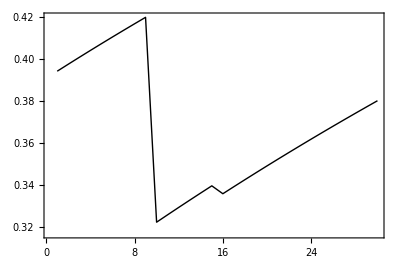

```mathematica
(* Accuracy for each Subscript[ω, m] *)
ListPlot[{Table[Abs[(keq.b4ωm[[i,2]]-keq.b4Theo[[i,2]])/(keq.b4ωm[[i,2]])]*100,{i,1,30}]},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"\\omega_m","\\text{Acc}\\%"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65]
```

```mathematica
(* Data for the GA *)
MockData=keq.b4ωm;
```

## Genetic Algorithm

## Grammar, Fitness Function, and Genetic Instructions

### Grammar

```mathematica
(* Possible operations. The proposal grammar depends on each specific problem *)
poly[x_]:=x
grammar={poly};(* Array of operations *)
```

### Genetic Code

```mathematica
length=4; depth=4; (* Number of nucleotides and genes. Chromosomes will be 4x4 matrices *)

(* Ranges to compute random numbers specifying the expression of an individual *)
rang1={0,9};  (* Overall coefficient of the expression *)
rang2={1,Length[grammar]}; (* To choose an operation in the grammar *)
rang3={0,9}; (* Coefficient of x *)
rang4={0,1}; (* Power of x *)
```

### Fitness Function

```mathematica
(* Accuracy of an Individual *)
AccGA[f_]:=AccGA[f]=Module[{temp,ft},
ft=(f/.{x->#1})&; (* Individual *)
temp=Mean[Table[Abs[MockData⟦i,2⟧-ft[MockData⟦i,1⟧]]/MockData⟦i,2⟧*100,{i,1,Length[MockData]}]]; (* Accuracy measure *)
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]] (* Space-Time constraints in the computation *)
```

## Genetic Operators

### Mutation

```mathematica
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]}; (* To decide where apply a mutation *)
mut=Which[
rep⟦2⟧==1,RandomReal[rang1], (* If rep⟦2⟧ == 1 -> modify the overall coefficient *)
rep⟦2⟧==2,RandomInteger[rang2], (* If rep⟦2⟧ == 2 -> modify the operation *)
rep⟦2⟧==3,RandomReal[rang3], (* If rep⟦2⟧ == 3 -> modify the coefficient of x *)
rep⟦2⟧==4,RandomReal[rang4]]; (* If rep⟦2⟧ == 4 -> modify the power of x *)
ReplacePart[kid,rep->mut]] (* Replace rep = {a, b} by mut = c in kid *)
```

### Crossover

```mathematica
cross[{kid1_,kid2_}]:=Module[{len},
len=RandomInteger[{1,length-1}]; (* Till length - 1 to not exceed the length of the chromosomes *)
{Join[kid1⟦1;;len⟧,kid2⟦(len+1);;-1⟧], (* Interchange of nucleotides *)
Join[kid1⟦(len+1);;-1⟧,kid2⟦1;;len⟧]}]
```

## Selection Scheme

### Tournament Selection

```mathematica
toursize=4; (* Participants in the tournament *)
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours], (* Take "tours" members from "fitnesses-set" at random *)
#1⟦1⟧>#2⟦1⟧&]⟦1,2⟧ (* Organize from greatest to smallest and take the individual with the best fit *)
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours], 
#1⟦1⟧>#2⟦1⟧&]⟦-1,2⟧ (* The same but taking the individual with the worst fit *)
```

## Genetic Algorithm

### Evolution of the Genetic Algorithm

```mathematica
selectionrate=0.3; (* Portion of the population to be sorted and replaced *)
(* Creator -> converts the chromosomes in "individuals" *)
funcGA[x_,kid_,gram_]:=Sum[kid[[i,1]] gram⟦kid⟦i,2⟧⟧@((kid[[i,3]]x)^kid⟦i,4⟧),{i,1,length}]  (* Default: no linear term *)
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2]; (* Around 1/3 of the population will be selected as the best *)
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={}; (* store: {fitness, individual, chromosome} *)

(* Progenitors -> Creation of "pop" chromosomes: 8 nucleotides for each gene and a total of 8 genes *)
chromosomes=Table[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomInteger[rang4]},{pop},{length}]; (* change by Integer *)
t1=AbsoluteTime[];

(* "pigs" is a "prior". It is computed for all pop. Its form depends on the problem *)
Do[pigs=funcGA[x,#,grammar]&/@chromosomes;
(* {-χ^2 for jth pig , counter j} sorted from the greatest to the smallest fitness *)
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[AccGA[pigs⟦j⟧],2,10^230],10^8,10^230],j},{j,1,Length[pigs]}],#1⟦1⟧>#2⟦1⟧&];

(* Append to bestfitperstep the greatest fitness, and its corresponding expression, and chromosomes *)
AppendTo[bestfitperstep,{fitness⟦1,1⟧,pigs⟦fitness⟦1,2⟧⟧,chromosomes⟦fitness⟦1,2⟧⟧}];

(* Selection of the best parents -> They are divided in pairs *)
p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];

(* Crossover of pairs *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes⟦p2⟦jj,1⟧⟧,chromosomes⟦p2⟦jj,2⟧⟧}], (* Worst are replaced by the children of the fittest *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

(* Mutation *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes⟦p2⟦jj,1⟧⟧],mutation[chromosomes⟦p2⟦jj,2⟧⟧]}, (* Worst are replaced by fittest mutations *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

prog`int++,{maxgens}];

If[verbose==True,
Print["Time taken: ",Round[AbsoluteTime[]-t1]," secs or ",Round[(AbsoluteTime[]-t1)/60], " mins"];
Print["Accuracy = ",Abs[fitness⟦1,1⟧]];
Print["Best-fit function is: "];
Print[bestfitperstep⟦-1,2⟧];
Speak["Listo el pollo"];];

bestfitperstep]
```

## Evolution

### Run

```mathematica
(* GA for Subscript[k, eq] *)
```

```mathematica
generations=500;
```

```mathematica
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, max generations, population, crossover-rate, mutation-rate, verbose (True/False)} *)
GApop=GAevo[9872,generations,100,0.7,0.35,True]//Quiet;(* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

Time taken: 17 secs or 0 mins

Accuracy = 0.0380626

Best-fit function is:

0.00428536 x^0.997509+0.0686118 x

```mathematica
(* EH formula is a line *)
keq[x]
AccGA[keq[x]]
```

0.0732106 x

0.367561

```mathematica
(* The GA suggest the following form *)
Winner[α_,β_,γ_,x_]:=α*x+γ*x^β
EH[δ_,x_]:=keq[x]-δ; (* Shift correction for the EH formula *)
χ2Winner[α_,β_,γ_]:=Mean[Table[Abs[MockData⟦i,2⟧-Winner[α,β,γ,MockData⟦i,1⟧]]/MockData⟦i,2⟧*100,{i,1,Length[MockData]}]]
χ2EH[δ_]:=Mean[Table[Abs[MockData⟦i,2⟧-EH[δ,MockData⟦i,1⟧]]/MockData⟦i,2⟧*100,{i,1,Length[MockData]}]]
FindMinimum[χ2Winner[α,β,γ],{{α,10^-2,10^-1},{β,0.01,2},{γ,10^-10,10^-3}}]
BestFit=%[[2]];
FindMinimum[χ2EH[δ],{δ,10^-5,1}] (* The GA is still more accurate *)
BestFitEH=%[[2]];
```

{0.0235603,{α→0.0722211,β→1.3775,γ→0.00150802}}

{0.0233437,{δ→0.0000378939}}

```mathematica
AccGA[0.07222x+0.00151*x^1.3775]
AccGA[0.0732106 x]
```

0.0235814

0.367557

### Plots

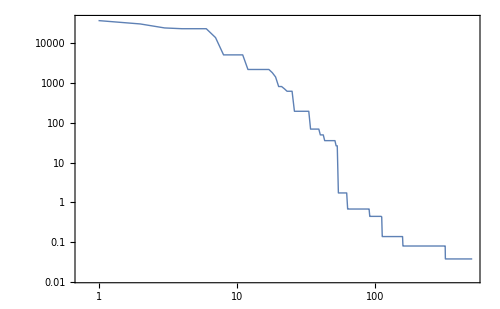

```mathematica
(* Plot of χ^2 over the generations *)
ListLogLogPlot[GApop[[All,1]]//Abs,Joined->True,
PlotRange->All,PlotStyle->Thick,
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\%\\mathrm{Acc}"},RotateLabel->True,BaseStyle->{FontFamily->"Times",FontSize->13},ImageSize->500]
```

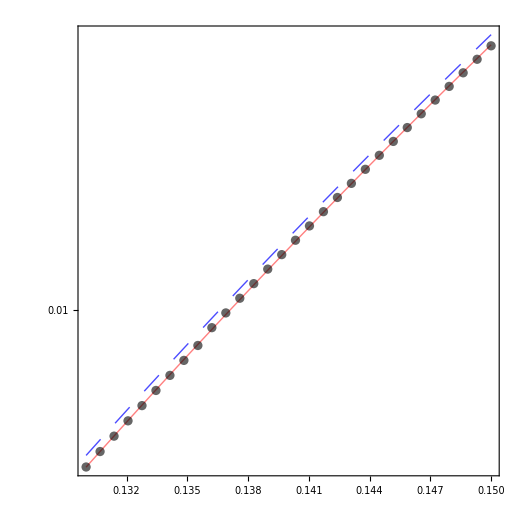

```mathematica
(* Best-Fit from the GA and the true function *)
ListLogPlot[{MockData},Joined->False,PlotRange->All,PlotStyle->{Directive[Black,Opacity[0.6]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->480,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{CLASS}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,5},LegendMarkerSize->30],
{0.7,0.2}]];
LogPlot[{Winner[α,β,γ,x]/.BestFit,keq[x]}//Evaluate,{x,MockData[[1,1]],MockData[[-1,1]]},PlotRange->All,PlotStyle->{Directive[Pink,Opacity[1],Thick],Directive[Blue,Dashing[0.03],Opacity[0.7],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\omega_m","k_\\text{eq} \\, [h / \\text{Mpc}]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{GA}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\text{EH}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendMarkerSize->30],
{0.7,0.32}],ImageSize->480];
Show[{%,%%},PlotRange->All,ImageSize->520,AspectRatio->1]
```

```mathematica
accGA=Table[{MockData⟦i,1⟧,100*Abs[(1-Winner[α,β,γ,MockData⟦i,1⟧]/MockData⟦i,2⟧)/.BestFit]},{i,1,Length[MockData]}];
accEH=Table[{MockData⟦i,1⟧,100*Abs[(1-keq[MockData⟦i,1⟧]/MockData⟦i,2⟧)]},{i,1,Length[MockData]}];
```

```mathematica
accGA
accEH
```

{{0.13,0.00524039},{0.13069,1.05516×10^-10},{0.13138,0.00519952},{0.13207,0.0103588},{0.13276,0.0154783},{0.13345,0.0205587},{0.13414,0.0256005},{0.13483,0.0306044},{0.13552,0.0355707},{0.13621,0.0601443},{0.1369,0.0547526},{0.13759,0.0494018},{0.13828,0.0440912},{0.13897,0.0388205},{0.13966,0.0335889},{0.14034,0.0355455},{0.14103,0.0303562},{0.14172,0.0252048},{0.14241,0.0200909},{0.1431,0.015014},{0.14379,0.00997351},{0.14448,0.00496901},{0.14517,1.13354×10^-11},{0.14586,0.00493397},{0.14655,0.00983336},{0.14724,0.0146986},{0.14793,0.0195302},{0.14862,0.0243285},{0.14931,0.029094},{0.15,0.0338271}}

{{0.13,0.394287},{0.13069,0.397625},{0.13138,0.400929},{0.13207,0.404199},{0.13276,0.407434},{0.13345,0.410637},{0.13414,0.413806},{0.13483,0.416944},{0.13552,0.42005},{0.13621,0.322095},{0.1369,0.325641},{0.13759,0.329152},{0.13828,0.332628},{0.13897,0.33607},{0.13966,0.339478},{0.14034,0.335703},{0.14103,0.33908},{0.14172,0.342424},{0.14241,0.345736},{0.1431,0.349016},{0.14379,0.352265},{0.14448,0.355483},{0.14517,0.358671},{0.14586,0.361828},{0.14655,0.364956},{0.14724,0.368056},{0.14793,0.371126},{0.14862,0.374168},{0.14931,0.377182},{0.15,0.380168}}

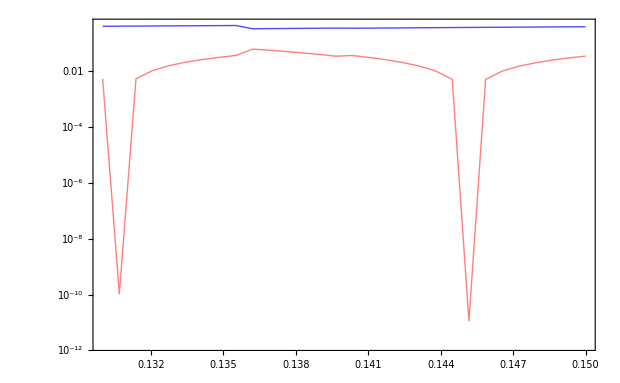

```mathematica
(* Comparison of the accuracies *)
ListLogPlot[{accGA,accEH},Joined->True,PlotRange->{{MockData⟦1,1⟧,MockData⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\omega_m","\\left|\\frac{k_{\\text{eq}, \\text{CLASS}} - k_{\\text{eq}, \\text{GA}}}{k_{\\text{eq}, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{Directive[Pink,Opacity[1],Thick],Directive[Blue,Opacity[0.7],Thick]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{GA}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{EH}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendFunction->None],
{0.4,0.2}],ImageSize->620]
```

# z_eq

```mathematica
Quit[]
```

## Data

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[8]; (* To use all the available kernels *)
```

### Data

```mathematica
MockData=Import["Data_k_z_eq.txt","Data"]//Quiet; (* {Subscript[ω, b], Subscript[ω, m], Subscript[k, eq], Subscript[z, eq]} *)
Dimensions[MockData] (* Dimensions of the dataset *)
```

{900,4}

#### Fitting Formula

```mathematica
(*All the formulas are extracted from EH97I[9709112 v1] paper,unless stated.*)
Θ=Solve[2.7*x==2.7255]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)
h=0.67810;
zeq[ωm_]:=2.5*10^4 ωm*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (2) *)
```

#### Comparison

```mathematica
(* Baryons do not modify Subscript[z, eq] *)
Table[{MockData[[i,2]],MockData[[i,4]]},{i,1,30}]-Table[{MockData[[i,2]],MockData[[i,4]]},{i,1+30,30+30}]
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

```mathematica
(* We only need the first 30 elements *)
zeq.b4ωm=Table[{MockData[[i,2]],MockData[[i,4]]},{i,1,30}];
zeq.b4Theo=Table[{MockData[[i,2]],zeq[MockData[[i,2]]]},{i,1,30}];
```

```mathematica
(* Mean accuracy of the EH formula *)
Mean[Table[Abs[zeq.b4ωm[[i,2]]-zeq.b4Theo[[i,2]]]/(zeq.b4ωm⟦i,2⟧)*100,{i,1,Length[zeq.b4ωm]}]]
```

0.736161

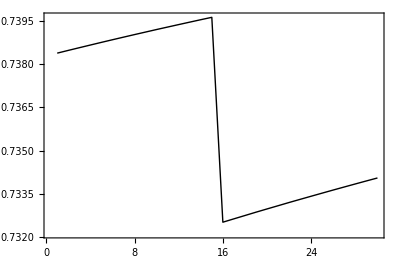

```mathematica
(* Accuracy for each Subscript[ω, m] *)
ListPlot[{Table[Abs[(zeq.b4ωm[[i,2]]-zeq.b4Theo[[i,2]])/(zeq.b4ωm[[i,2]])]*100,{i,1,30}]},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"\\omega_m","\\text{Acc}\\%"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65]
```

```mathematica
(* Data for the GA *)
MockData=zeq.b4ωm;
```

## Genetic Algorithm

## Grammar, Fitness Function, and Genetic Instructions

### Grammar

```mathematica
(* Possible operations. The proposal grammar depends on each specific problem *)
poly[x_]:=x
grammar={poly};(* Array of operations *)
```

### Genetic Code

```mathematica
length=4; depth=4; (* Number of nucleotides and genes. Chromosomes will be 4x4 matrices *)

(* Ranges to compute random numbers specifying the expression of an individual *)
rang1={0,9};  (* Overall coefficient of the expression *)
rang2={1,Length[grammar]}; (* To choose an operation in the grammar *)
rang3={0,9}; (* Coefficient of x *)
rang4={0,1}; (* Power of x *)
```

### Fitness Function

```mathematica
(* Accuracy of an Individual *)
AccGA[f_]:=AccGA[f]=Module[{temp,ft},
ft=(f/.{x->#1})&; (* Individual *)
temp=Mean[Table[Abs[MockData⟦i,2⟧-ft[MockData⟦i,1⟧]]/MockData⟦i,2⟧*100,{i,1,Length[MockData]}]]; (* Accuracy measure *)
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]] (* Space-Time constraints in the computation *)
```

## Genetic Operators

### Mutation

```mathematica
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]}; (* To decide where apply a mutation *)
mut=Which[
rep⟦2⟧==1,RandomReal[rang1], (* If rep⟦2⟧ == 1 -> modify the overall coefficient *)
rep⟦2⟧==2,RandomInteger[rang2], (* If rep⟦2⟧ == 2 -> modify the operation *)
rep⟦2⟧==3,RandomReal[rang3], (* If rep⟦2⟧ == 3 -> modify the coefficient of x *)
rep⟦2⟧==4,RandomReal[rang4]]; (* If rep⟦2⟧ == 4 -> modify the power of x *)
ReplacePart[kid,rep->mut]] (* Replace rep = {a, b} by mut = c in kid *)
```

### Crossover

```mathematica
cross[{kid1_,kid2_}]:=Module[{len},
len=RandomInteger[{1,length-1}]; (* Till length - 1 to not exceed the length of the chromosomes *)
{Join[kid1⟦1;;len⟧,kid2⟦(len+1);;-1⟧], (* Interchange of nucleotides *)
Join[kid1⟦(len+1);;-1⟧,kid2⟦1;;len⟧]}]
```

## Selection Scheme

### Tournament Selection

```mathematica
toursize=4; (* Participants in the tournament *)
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours], (* Take "tours" members from "fitnesses-set" at random *)
#1⟦1⟧>#2⟦1⟧&]⟦1,2⟧ (* Organize from greatest to smallest and take the individual with the best fit *)
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours], 
#1⟦1⟧>#2⟦1⟧&]⟦-1,2⟧ (* The same but taking the individual with the worst fit *)
```

## Genetic Algorithm

### Evolution of the Genetic Algorithm

```mathematica
selectionrate=0.3; (* Portion of the population to be sorted and replaced *)
(* Creator -> converts the chromosomes in "individuals" *)
funcGA[x_,kid_,gram_]:=Sum[kid[[i,1]] gram⟦kid⟦i,2⟧⟧@((kid[[i,3]]x)^kid⟦i,4⟧),{i,1,length}]  (* Default: no linear term *)
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2]; (* Around 1/3 of the population will be selected as the best *)
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={}; (* store: {fitness, individual, chromosome} *)

(* Progenitors -> Creation of "pop" chromosomes: 8 nucleotides for each gene and a total of 8 genes *)
chromosomes=Table[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomInteger[rang4]},{pop},{length}]; (* change by Integer *)
t1=AbsoluteTime[];

(* "pigs" is a "prior". It is computed for all pop. Its form depends on the problem. *)
Do[pigs=3*10^5 funcGA[x,#,grammar]&/@chromosomes;
(* {-χ^2 for jth pig , counter j} sorted from the greatest to the smallest fitness *)
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[AccGA[pigs⟦j⟧],2,10^230],10^8,10^230],j},{j,1,Length[pigs]}],#1⟦1⟧>#2⟦1⟧&];

(* Append to bestfitperstep the greatest fitness, and its corresponding expression, and chromosomes *)
AppendTo[bestfitperstep,{fitness⟦1,1⟧,pigs⟦fitness⟦1,2⟧⟧,chromosomes⟦fitness⟦1,2⟧⟧}];

(* Selection of the best parents -> They are divided in pairs *)
p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];

(* Crossover of pairs *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes⟦p2⟦jj,1⟧⟧,chromosomes⟦p2⟦jj,2⟧⟧}], (* Worst are replaced by the children of the fittest *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

(* Mutation *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes⟦p2⟦jj,1⟧⟧],mutation[chromosomes⟦p2⟦jj,2⟧⟧]}, (* Worst are replaced by fittest mutations *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

prog`int++,{maxgens}];

If[verbose==True,
Print["Time taken: ",Round[AbsoluteTime[]-t1]," secs or ",Round[(AbsoluteTime[]-t1)/60], " mins"];
Print["Accuracy = ",Abs[fitness⟦1,1⟧]];
Print["Best-fit function is: "];
Print[bestfitperstep⟦-1,2⟧];
Speak["Listo el pollo"];];

bestfitperstep]
```

## Evolution

### Run

```mathematica
(* GA for Subscript[z, eq] *)
```

```mathematica
generations=500;
```

```mathematica
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, max generations, population, crossover-rate, mutation-rate, verbose (True/False)} *)
GApop=GAevo[9872,generations,100,0.7,0.35,True]//Quiet;(* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

Time taken: 19 secs or 0 mins

Accuracy = 0.00468717

Best-fit function is:

300000 (0.000262407 x^0.983837+0.0264656 x^0.999997+0.0529312 x)

```mathematica
(* EH formula is a line *)
zeq[x]
AccGA[zeq[x]]
```

24077.4 x

0.736161

```mathematica
(* The GA suggest the following form -> It is not merely a shift *)
Winner[α_,β_,γ_,x_]:=α*x+γ*x^β
EH[δ_,x_]:=zeq[x]-δ; (* Shift correction for the EH formula *)
χ2Winner[α_,β_,γ_]:=Mean[Table[Abs[MockData⟦i,2⟧-Winner[α,β,γ,MockData⟦i,1⟧]]/MockData⟦i,2⟧*100,{i,1,Length[MockData]}]]
χ2EH[δ_]:=Mean[Table[Abs[MockData⟦i,2⟧-EH[δ,MockData⟦i,1⟧]]/MockData⟦i,2⟧*100,{i,1,Length[MockData]}]]
FindMinimum[χ2Winner[α,β,γ],{{α,10^-2,10^-1},{β,0.01,2},{γ,10^-10,10^-3}}]
BestFit=%[[2]];
FindMinimum[χ2EH[δ],{δ,10^-5,1}] (* The GA is still more accurate *)
BestFitEH=%[[2]];
```

{0.00250264,{α→23896.7,β→1.41595,γ→11.6353}}

{0.0245909,{δ→24.5723}}

### Plots

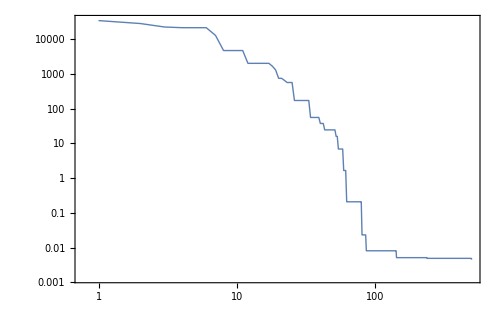

```mathematica
(* Plot of χ^2 over the generations -> We should modify the configuration of the GA *)
ListLogLogPlot[GApop[[All,1]]//Abs,Joined->True,
PlotRange->All,PlotStyle->Thick,
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\%\\mathrm{Acc}"},RotateLabel->True,BaseStyle->{FontFamily->"Times",FontSize->13},ImageSize->500]
```

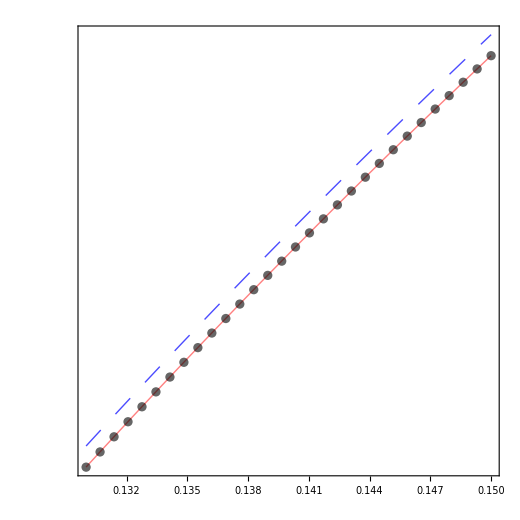

```mathematica
(* Best-Fit from the GA and the true function *)
ListLogPlot[{MockData},Joined->False,PlotRange->All,PlotStyle->{Directive[Black,Opacity[0.6]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","P(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->480,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{CLASS}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,10},LegendMarkerSize->30],
{0.7,0.2}]];
LogPlot[{Winner[α,β,γ,x]/.BestFit,zeq[x]}//Evaluate,{x,MockData[[1,1]],MockData[[-1,1]]},PlotRange->All,PlotStyle->{Directive[Pink,Opacity[1],Thick],Directive[Blue,Dashing[0.03],Opacity[0.7],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"\\omega_m","z_\\text{eq}"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.4]&)/@Style["\\text{GA}"],
(MaTeX[#,Magnification->1.4]&)/@Style["\\text{EH}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendMarkerSize->{40,25}],
{0.7,0.32}],ImageSize->480];
Show[{%,%%},PlotRange->All,ImageSize->520,AspectRatio->1]
```

```mathematica
accGA=Table[{MockData⟦i,1⟧,100*Abs[(1-Winner[α,β,γ,MockData⟦i,1⟧]/MockData⟦i,2⟧)/.BestFit]},{i,1,Length[MockData]}];
accEH=Table[{MockData⟦i,1⟧,100*Abs[(1-zeq[MockData⟦i,1⟧]/MockData⟦i,2⟧)]},{i,1,Length[MockData]}];
```

```mathematica
accGA
accEH
```

{{0.13,0.00301378},{0.13069,0.00315392},{0.13138,0.00329229},{0.13207,0.00342987},{0.13276,0.00356699},{0.13345,0.00370239},{0.13414,0.00383674},{0.13483,0.00397034},{0.13552,0.00410229},{0.13621,0.00423446},{0.1369,0.00436409},{0.13759,0.00449334},{0.13828,0.00462192},{0.13897,0.00474983},{0.13966,0.00487589},{0.14034,0.00212442},{0.14103,0.00196536},{0.14172,0.00180725},{0.14241,0.00164891},{0.1431,0.00149384},{0.14379,0.00133996},{0.14448,0.00118523},{0.14517,0.00103399},{0.14586,0.000883314},{0.14655,0.000733485},{0.14724,0.000584207},{0.14793,0.000436887},{0.14862,0.000290092},{0.14931,0.000144094},{0.15,1.11022×10^-14}}

{{0.13,0.738381},{0.13069,0.738476},{0.13138,0.738569},{0.13207,0.738662},{0.13276,0.738754},{0.13345,0.738845},{0.13414,0.738934},{0.13483,0.739024},{0.13552,0.739111},{0.13621,0.739199},{0.1369,0.739285},{0.13759,0.73937},{0.13828,0.739455},{0.13897,0.739539},{0.13966,0.739622},{0.14034,0.732526},{0.14103,0.732642},{0.14172,0.732757},{0.14241,0.732873},{0.1431,0.732985},{0.14379,0.733096},{0.14448,0.733209},{0.14517,0.733317},{0.14586,0.733426},{0.14655,0.733533},{0.14724,0.733641},{0.14793,0.733746},{0.14862,0.733851},{0.14931,0.733955},{0.15,0.734058}}

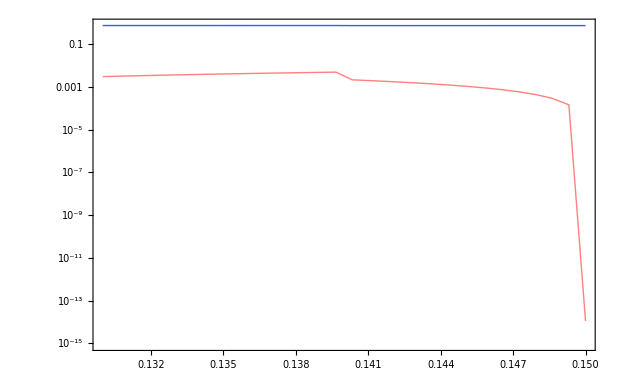

```mathematica
(* Comparison of the accuracies *)
ListLogPlot[{accGA,accEH},Joined->True,PlotRange->{{MockData⟦1,1⟧,MockData⟦-1,1⟧},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"\\omega_m","\\left|\\frac{z_{\\text{eq}, \\text{CLASS}} - z_{\\text{eq}, \\text{GA}}}{z_{\\text{eq}, \\text{CLASS}}}\\right| \\times 100"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotStyle->{Directive[Pink,Opacity[1],Thick],Directive[Blue,Opacity[0.7],Thick]},PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.5]&)/@Style["\\text{GA}"],
(MaTeX[#,Magnification->1.5]&)/@Style["\\text{EH}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,15},LegendFunction->None],
{0.4,0.2}],ImageSize->620]
```